## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TKT2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp2.csv";

mainFolder = "fit_TKT2_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{e4p,Null;xu5p__D,Null,Keq substrate}

{59.6,Keq value}

{e4p,Km or S05 substrate}

{0.00009,Km or S05 value}

{xu5p__D,Km or S05 substrate}

{0.00016,Km or S05 value}

(e4p^c+xu5p__D^c⇌f6p^c+g3p^c)^TKT2

Ping Pong Bi Bi; xu5p-D,g3p,e4p,f6p

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;xu5p__D,Null | 59.6 | 56.62
62.58 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | 0.00009 | 0.0000855
0.0000945 | xu5p__D | 0.016
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg | 0.005
cl | 0.01
1 | xu5p__D | 0.00016 | 0.000152
0.000168 | e4p | 0.009
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg | 0.005
cl | 0.01

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities ={1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+xu5p__D^c⇌f6p^c+g3p^c)^TKT2

Ping Pong Bi Bi; xu5p-D,g3p,e4p,f6p

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p,Null;xu5p__D,Null | 59.6 | 56.62
62.58 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | 0.00009 | 0.0000855
0.0000945 | xu5p__D | 0.016
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg | 0.005
cl | 0.01
1 | xu5p__D | 0.00016 | 0.000152
0.000168 | e4p | 0.009
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg | 0.005
cl | 0.01

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TKT2[c] + xu5p__D[c] <=> E_TKT2[c]&xu5p__D",
				"E_TKT2[c]&xu5p__D <=> E_TKT2[c]&g3p",
				"E_TKT2[c]&g3p <=> E_TKT2[c] + g3p[c]",

				"E_TKT2[c] + e4p[c] <=> E_TKT2[c]&e4p",
				"E_TKT2[c]&e4p <=> E_TKT2[c]&f6p",
				"E_TKT2[c]&f6p <=> E_TKT2[c] + f6p[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TKT2^c)_^+e4p^c⇌(TKT2^c&e4p^c)_^)^TKT21,((TKT2^c)_^+xu5p__D^c⇌(TKT2^c&xu5p_^D)_^)^TKT22,((TKT2^c&f6p^c)_^⇌(TKT2^c)_^+f6p^c)^TKT23,((TKT2^c&e4p^c)_^⇌(TKT2^c&f6p^c)_^)^TKT24,((TKT2^c&g3p^c)_^⇌(TKT2^c)_^+g3p^c)^TKT25,((TKT2^c&xu5p_^D)_^⇌(TKT2^c&g3p^c)_^)^TKT26}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TKT2^c)_^+e4p^c⇌(TKT2^c&e4p^c)_^)^TKT21,((TKT2^c)_^+xu5p__D^c⇌(TKT2^c&xu5p_^D)_^)^TKT22,Overscript[(TKT2^c&f6p^c)_^⇌(TKT2^c)_^+f6p^c, TKT23],((TKT2^c&e4p^c)_^⇌(TKT2^c&f6p^c)_^)^TKT24,Overscript[(TKT2^c&g3p^c)_^⇌(TKT2^c)_^+g3p^c, TKT25],((TKT2^c&xu5p_^D)_^⇌(TKT2^c&g3p^c)_^)^TKT26};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{e4p^c→0,xu5p__D^c→0}

{f6p^c→0,g3p^c→0}

{e4p^c→∞,xu5p__D^c→∞}

{f6p^c→∞,g3p^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((TKT2^c&e4p^c)_^-((TKT2^c&f6p^c)_^)/K_TKT24) Volume_c k_TKT24^⟶,((TKT2^c&xu5p_^D)_^-((TKT2^c&g3p^c)_^)/K_TKT26) Volume_c k_TKT26^⟶}

Volume_c (-(TKT2^c&f6p^c)_^ k_TKT24^⟵+(TKT2^c&e4p^c)_^ k_TKT24^⟶-(TKT2^c&g3p^c)_^ k_TKT26^⟵+(TKT2^c&xu5p_^D)_^ k_TKT26^⟶)

1

2

3

0.453859

4

0.00183

5

0.00031

Simplifying...

6

0.549498

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Part::partw: Part 1 of {} does not exist.

```mathematica
FilePrint@dataPathList
```

Priority	e4p[c]	f6p[c]	g3p[c]	xu5p__D[c]	param_TKT2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt"	59.6
1	9.000000000000007e-6	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.09090909090909098
1	0.000014264038732150038	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.13680688860321014
1	0.000022606977883586257	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.20076000891310197
1	0.00003582964534981475	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.2847472489508014
1	0.00005678616100321741	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.38686317984685703
1	0.00009000000000000007	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.5000000000000002
1	0.00014264038732150037	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.6131368201531432
1	0.00022606977883586258	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.7152527510491988
1	0.00035829645349814786	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.7992399910868985
1	0.0005678616100321741	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.86319311139679
1	0.0009000000000000007	0	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt"	0.9090909090909093
1	0.009	0	0	0.00001600000000000001	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.09090909090909095
1	0.009	0	0	0.00002535829107937784	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.13680688860321008
1	0.009	0	0	0.00004019018290415334	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.20076000891310194
1	0.009	0	0	0.00006369714728855955	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.28474724895080133
1	0.009	0	0	0.00010095317511683093	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.386863179846857
1	0.009	0	0	0.0001600000000000001	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.5000000000000001
1	0.009	0	0	0.0002535829107937784	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.6131368201531433
1	0.009	0	0	0.00040190182904153337	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.7152527510491988
1	0.009	0	0	0.0006369714728855961	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.7992399910868984
1	0.009	0	0	0.0010095317511683093	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.86319311139679
1	0.009	0	0	0.001600000000000001	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt"	0.9090909090909092

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.17917703105
best_fit: 1.17917699754
best_fit: 1.17917704217
best_fit: 1.17917701398
best_fit: 4.1361677564
best_fit: 1.17917699281
best_fit: 1.17917811977
best_fit: 4.13616770864
best_fit: 1.17917717279
best_fit: 1.17917702015

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | haldaneRatio_1 | 8.15946×10^-7 | 6.65768×10^-13 | 0.000111976 | 0.000187878 | 59.6 | 59.5999
1 | relRateFor_e4p | 4.01524×10^-6 | 1.61222×10^-11 | 8.4049×10^-7 | 0.000924539 | 0.0909091 | 0.0909083
1 | relRateFor_e4p | 3.81253×10^-6 | 1.45353×10^-11 | 1.20098×10^-6 | 0.000877863 | 0.136807 | 0.136806
1 | relRateFor_e4p | 3.53006×10^-6 | 1.24613×10^-11 | 1.63182×10^-6 | 0.000812823 | 0.20076 | 0.200758
1 | relRateFor_e4p | 3.15911×10^-6 | 9.97998×10^-12 | 2.07128×10^-6 | 0.000727409 | 0.284747 | 0.284745
1 | relRateFor_e4p | 2.70809×10^-6 | 7.33375×10^-12 | 2.41232×10^-6 | 0.000623559 | 0.386863 | 0.386861
1 | relRateFor_e4p | 2.20839×10^-6 | 4.87699×10^-12 | 2.5425×10^-6 | 0.000508499 | 0.5 | 0.499997
1 | relRateFor_e4p | 1.70869×10^-6 | 2.91962×10^-12 | 2.41232×10^-6 | 0.00039344 | 0.613137 | 0.613134
1 | relRateFor_e4p | 1.25767×10^-6 | 1.58173×10^-12 | 2.07129×10^-6 | 0.000289588 | 0.715253 | 0.715251
1 | relRateFor_e4p | 8.86714×10^-7 | 7.86262×10^-13 | 1.63183×10^-6 | 0.000204173 | 0.79924 | 0.799238
1 | relRateFor_e4p | 6.04247×10^-7 | 3.65115×10^-13 | 1.20099×10^-6 | 0.000139133 | 0.863193 | 0.863192
1 | relRateFor_e4p | 4.01526×10^-7 | 1.61223×10^-13 | 8.40498×10^-7 | 0.0000924548 | 0.909091 | 0.90909
1 | relRateFor_xu5p__D | 0.639372 | 0.408797 | 0.30535 | 335.885 | 0.0909091 | 0.396259
1 | relRateFor_xu5p__D | 0.461872 | 0.213325 | 0.259452 | 189.649 | 0.136807 | 0.396259
1 | relRateFor_xu5p__D | 0.295302 | 0.0872035 | 0.195499 | 97.3796 | 0.20076 | 0.396259
1 | relRateFor_xu5p__D | 0.14352 | 0.020598 | 0.111512 | 39.1618 | 0.284747 | 0.396259
1 | relRateFor_xu5p__D | 0.0104222 | 0.000108621 | 0.0093962 | 2.42882 | 0.386863 | 0.396259
1 | relRateFor_xu5p__D | 0.10099 | 0.0101991 | 0.103741 | 20.7481 | 0.5 | 0.396259
1 | relRateFor_xu5p__D | 0.189578 | 0.0359398 | 0.216877 | 35.3718 | 0.613137 | 0.396259
1 | relRateFor_xu5p__D | 0.25648 | 0.065782 | 0.318993 | 44.5987 | 0.715253 | 0.396259
1 | relRateFor_xu5p__D | 0.304698 | 0.0928407 | 0.402981 | 50.4205 | 0.79924 | 0.396259
1 | relRateFor_xu5p__D | 0.338128 | 0.114331 | 0.466934 | 54.0938 | 0.863193 | 0.396259
1 | relRateFor_xu5p__D | 0.360628 | 0.130052 | 0.512832 | 56.4115 | 0.909091 | 0.396259

### Simulated Data and Best Fit Data Plot

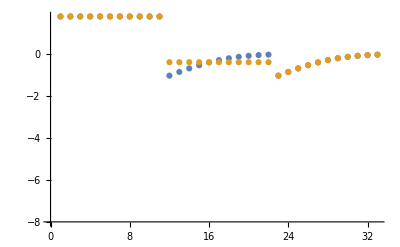

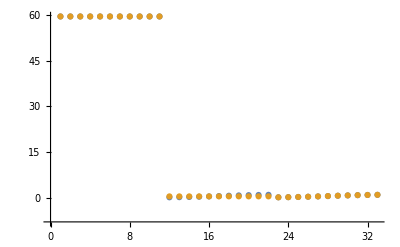

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

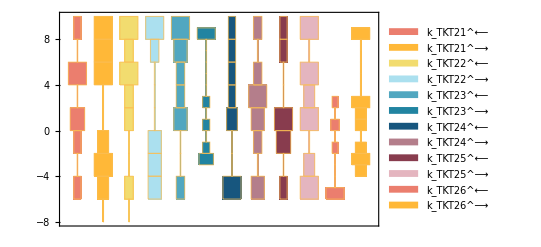

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

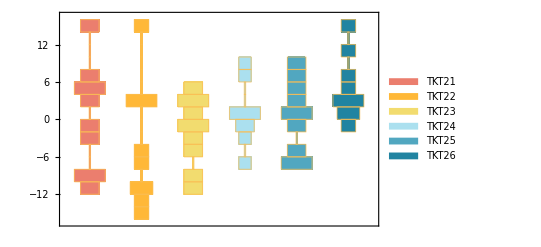

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

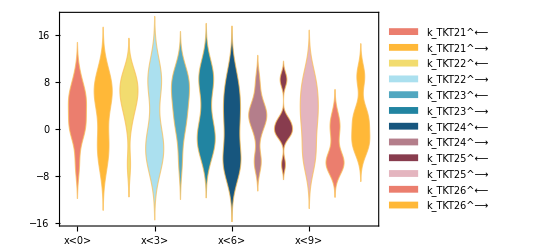

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

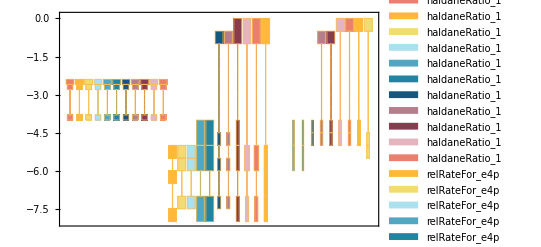

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(e4p^c+xu5p__D^c⇌f6p^c+g3p^c)^TKT2,{{1,e4p,0.00009,{0.0000855,0.0000945},{{xu5p__D,0.016},{thmpp,0.001}},M,8.5,30,{{glygly,0.05}},{{mg,0.005},{cl,0.01}}},{1,xu5p__D,0.00016,{0.000152,0.000168},{{e4p,0.009},{thmpp,0.001}},M,8.5,30,{{glygly,0.05}},{{mg,0.005},{cl,0.01}}}},{((k_TKT23^⟶+k_TKT24^⟵+k_TKT24^⟶) (xu5p__D^c k_TKT22^⟶ (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟶ k_TKT26^⟶+e4p^c k_TKT21^⟶ k_TKT23^⟶ k_TKT24^⟶ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)))/(k_TKT23^⟶ k_TKT24^⟶ (e4p^c k_TKT21^⟶ (k_TKT23^⟶+k_TKT24^⟵+k_TKT24^⟶) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)+k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶+xu5p__D^c k_TKT22^⟶ (k_TKT25^⟶+k_TKT26^⟵+k_TKT26^⟶))+k_TKT23^⟶ k_TKT24^⟶ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶+xu5p__D^c k_TKT22^⟶ (k_TKT25^⟶+k_TKT26^⟵+k_TKT26^⟶)))),((k_TKT25^⟶+k_TKT26^⟵+k_TKT26^⟶) (xu5p__D^c k_TKT22^⟶ (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟶ k_TKT26^⟶+e4p^c k_TKT21^⟶ k_TKT23^⟶ k_TKT24^⟶ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)))/(k_TKT25^⟶ k_TKT26^⟶ (e4p^c k_TKT21^⟶ (k_TKT23^⟶+k_TKT24^⟵+k_TKT24^⟶) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)+k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶+xu5p__D^c k_TKT22^⟶ (k_TKT25^⟶+k_TKT26^⟵+k_TKT26^⟶))+k_TKT23^⟶ k_TKT24^⟶ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶+xu5p__D^c k_TKT22^⟶ (k_TKT25^⟶+k_TKT26^⟵+k_TKT26^⟶))))},{((k_TKT21^⟵+k_TKT24^⟵+k_TKT24^⟶) (g3p^c k_TKT22^⟵ (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟵ k_TKT26^⟵+f6p^c k_TKT21^⟵ k_TKT23^⟵ k_TKT24^⟵ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)))/(k_TKT21^⟵ k_TKT24^⟵ (g3p^c (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟵ (k_TKT22^⟵+k_TKT26^⟵+k_TKT26^⟶)+(k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶+f6p^c k_TKT23^⟵ (k_TKT21^⟵+k_TKT24^⟵+k_TKT24^⟶)) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶))),((k_TKT22^⟵+k_TKT26^⟵+k_TKT26^⟶) (g3p^c k_TKT22^⟵ (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟵ k_TKT26^⟵+f6p^c k_TKT21^⟵ k_TKT23^⟵ k_TKT24^⟵ (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)))/(k_TKT22^⟵ k_TKT26^⟵ (g3p^c (k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶) k_TKT25^⟵ (k_TKT22^⟵+k_TKT26^⟵+k_TKT26^⟶)+(k_TKT21^⟵ (k_TKT23^⟶+k_TKT24^⟵)+k_TKT23^⟶ k_TKT24^⟶+f6p^c k_TKT23^⟵ (k_TKT21^⟵+k_TKT24^⟵+k_TKT24^⟶)) (k_TKT22^⟵ (k_TKT25^⟶+k_TKT26^⟵)+k_TKT25^⟶ k_TKT26^⟶)))},{e4p^c→∞,xu5p__D^c→∞},{f6p^c→∞,g3p^c→∞},{k_TKT21^⟵→5.52889,k_TKT21^⟶→19050.9,k_TKT22^⟵→9.46138×10^6,k_TKT22^⟶→0.00029199,k_TKT23^⟵→26642.8,k_TKT23^⟶→1.29361,k_TKT24^⟵→2.96361×10^-6,k_TKT24^⟶→11.7208,k_TKT25^⟵→1.38823,k_TKT25^⟶→1.70398×10^8,k_TKT26^⟵→122.418,k_TKT26^⟶→2.91096},1,TKT2]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
59.6 | 59.5999 | 0.000187878

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
59.6 | 59.5999 | 0.000187878

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,9.×10^-6,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.0909091},{1,0.000014264,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.136807},{1,0.000022607,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.20076},{1,0.0000358296,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.284747},{1,0.0000567862,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.386863},{1,0.00009,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.5},{1,0.00014264,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.613137},{1,0.00022607,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.715253},{1,0.000358296,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.79924},{1,0.000567862,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.863193},{1,0.0009,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.909091},{1,0.009,0,0,0.000016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.0909091},{1,0.009,0,0,0.0000253583,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.136807},{1,0.009,0,0,0.0000401902,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.20076},{1,0.009,0,0,0.0000636971,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.284747},{1,0.009,0,0,0.000100953,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.386863},{1,0.009,0,0,0.00016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.5},{1,0.009,0,0,0.000253583,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.613137},{1,0.009,0,0,0.000401902,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.715253},{1,0.009,0,0,0.000636971,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.79924},{1,0.009,0,0,0.00100953,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.863193},{1,0.009,0,0,0.0016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.909091}},{1.17918,{5.52889,19050.9,9.46138×10^6,0.00029199,26642.8,1.29361,2.96361×10^-6,11.7208,1.38823,1.70398×10^8,122.418,2.91096},{59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,0.0909083,0.136806,0.200758,0.284745,0.386861,0.499997,0.613134,0.715251,0.799238,0.863192,0.90909,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259}},{Priority,e4p[c],f6p[c],g3p[c],xu5p__D[c],param_TKT2_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/haldaneRatio_1.txt,59.6},{1,9.×10^-6,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.0909091},{1,0.000014264,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.136807},{1,0.000022607,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.20076},{1,0.0000358296,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.284747},{1,0.0000567862,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.386863},{1,0.00009,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.5},{1,0.00014264,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.613137},{1,0.00022607,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.715253},{1,0.000358296,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.79924},{1,0.000567862,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.863193},{1,0.0009,0,0,0.016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_e4p.txt,0.909091},{1,0.009,0,0,0.000016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.0909091},{1,0.009,0,0,0.0000253583,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.136807},{1,0.009,0,0,0.0000401902,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.20076},{1,0.009,0,0,0.0000636971,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.284747},{1,0.009,0,0,0.000100953,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.386863},{1,0.009,0,0,0.00016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.5},{1,0.009,0,0,0.000253583,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.613137},{1,0.009,0,0,0.000401902,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.715253},{1,0.009,0,0,0.000636971,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.79924},{1,0.009,0,0,0.00100953,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.863193},{1,0.009,0,0,0.0016,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT2_typeII/input/relRateFor_xu5p__D.txt,0.909091}},{1.17918,{5.52889,19050.9,9.46138×10^6,0.00029199,26642.8,1.29361,2.96361×10^-6,11.7208,1.38823,1.70398×10^8,122.418,2.91096},{59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,59.5999,0.0909083,0.136806,0.200758,0.284745,0.386861,0.499997,0.613134,0.715251,0.799238,0.863192,0.90909,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259,0.396259}},{Priority,e4p[c],f6p[c],g3p[c],xu5p__D[c],param_TKT2_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(e4p^c+xu5p__D^c⇌f6p^c+g3p^c)^TKT2,TKT2,«20»,{Priority,e4p[c],f6p[c],g3p[c],xu5p__D[c],param_TKT2_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]